```mathematica
f[l_, h_]:=1/(2Pi)( l/h Log[1+h^2/l^2]-h/l Log[1+l^2/h^2]+4  ArcTan[l/h] ) 
f[5,5]//N
```

0.5

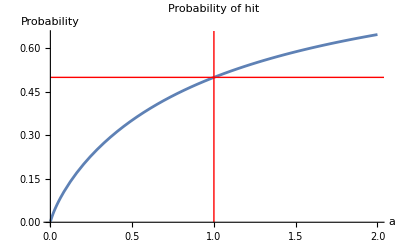

```mathematica
f[a_]:=(2Pi)^-1(a Log[1+a^-2]-a^-1 Log[1+a^2]+4ArcTan[a])
Plot[f[a],{a,0.001,2},Epilog->{Red,Line[{{1,0},{1,1}}],Line[{{0,0.5},{3,0.5}}]},AxesLabel->{"a","Probability"},PlotLabel->"Probability of hit"]
```

```mathematica
a=1;
k=4;
Sqrt[f[a/k]]//N
```

0.479681

```mathematica
FullSimplify[1/(2Pi)( l/h Log[1+h^2/l^2]-h/l Log[1+l^2/h^2]+4  ArcTan[l/h] ) /.{l->L/k},Assumptions->{h>0,l>0,k>0}]
```

(4 ArcCot[(2 h)/L]+(L Log[1+(4 h^2)/L^2])/(2 h)-(2 h Log[1+L^2/(4 h^2)])/L)/(2 π)

```mathematica
FullSimplify[(2Pi)^-1(a Log[1+a^-2]-a^-1 Log[1+a^2]+4ArcTan[a])/.{a->a/k},Assumptions->{a>0,k>0}]
```

(4 ArcTan[a/k]-(k Log[1+a^2/k^2])/a+(a Log[1+k^2/a^2])/k)/(2 π)

0.741086

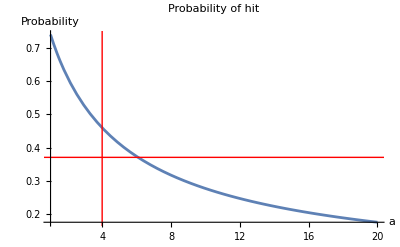

```mathematica
f[l_, h_]:=1/(2Pi)( l/h Log[1+h^2/l^2]-h/l Log[1+l^2/h^2]+4  ArcTan[l/h] ) 
L=10;
H=3;
start = f[L,H]//N
Plot[f[L/k,H],{k,1,20},Epilog->{Red,Line[{{4,0},{4,1}}],Line[{{0,start/2},{100,start/2}}]},AxesLabel->{"a","Probability"},PlotLabel->"Probability of hit"]
```

```mathematica
FullSimplify[(1+x)(1+x^-1)]
```

2+1/x+x

```mathematica
FullSimplify[(1+H^2/L^2)^(L/H)(1+L^2/H^2)^(-H/L),Assumptions->{L>0,H>0}]
```

(1+H^2/L^2)^(L/H) (1+L^2/H^2)^(-H/L)

```mathematica
FullSimplify[(1+a^-2)^a(1+a^2)^(-a^-1),Assumptions->{a>0}]
```

a^(-2 a) (1+a^2)^(-1/a+a)

```mathematica
a^(-2 a) (1+a^2)^(-1/a+a)/.{a->L/H}
```

(L/H)^(-(2 L)/H) (1+L^2/H^2)^(-H/L+L/H)

```mathematica
FullSimplify[(L/H)^(-(2 L)/H) (1+L^2/H^2)^(-H/L+L/H)]
```

(L/H)^(-(2 L)/H) (1+L^2/H^2)^(-H/L+L/H)

```mathematica
FullSimplify[Log[(L/H)^(-(2 L)/H) (1+L^2/H^2)^(-H/L+L/H)],{L>0,H>0}]
```

(2 L Log[H/L])/H+(-H/L+L/H) Log[1+L^2/H^2]

```mathematica
(2 L Log[H/L])/H+(-H/L+L/H) Log[1+L^2/H^2] - ( L/H Log[1+H^2/L^2]-H/L Log[1+L^2/H^2])/.{L->10,H->5}
```

-2 Log[5/4]-4 Log[2]+2 Log[5]

```mathematica
FullSimplify[(2 L Log[H/L])/H + L/H Log[1+L^2/H^2]]
```

(2 L Log[H/L])/H+(L Log[1+L^2/H^2])/H